```mathematica
NS["mcmc_sufficiency_posteriors","C:\\Users\\pglpm\\repositories\\neurobayes\\"];
```

```mathematica
(* Examination of formulae from "luca181219-sufficiency_posteriors" via Monte Carlo sampling *)
```

```mathematica
xlny[x_,y_]:=If[x>0,x*Log[y],0];SetAttributes[xlny,Listable];
hx[a_,b_]:=Total[xlny[a,b]];
hh[a_,b_]:=Total[xlny[a,a/b]];
```

```mathematica
nn=1000;
n=100;
gg[s_,ss_]=Binomial[n,s]*Binomial[nn-n,ss-s]/Binomial[nn,ss];
```

```mathematica
(* statistics *)
cc[r_,ss_]=Binomial[ss,r]/Binomial[nn,r];
```

```mathematica
(* check with two moments *)
ll={20,-3000};
pss=N[(#/Total@#)&@Table[Binomial[nn,ss]*Exp[Sum[cc[r,ss]*ll[[r]],{r,1,2}]],{ss,0,nn}]];ListPlot[T@{Range[0,nn]/nn,pss},Joined->True, PlotRange->All,ImageSize->a4longside/2]
```

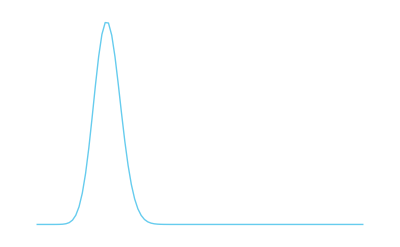

```mathematica
ps=(#/Total@#)&@Table[Sum[gg[s,ss]*pss[[ss+1]],{ss,0,nn}],{s,0,n}];
ListPlot[T@{Range[0,n]/n,ps},Joined->True, PlotRange->All,ImageSize->a4longside/2]
```

```mathematica
hx[a_,b_]:=Total[xlny[a,b]];
hh[a_,b_]:=Total[xlny[a,a/b]];
```

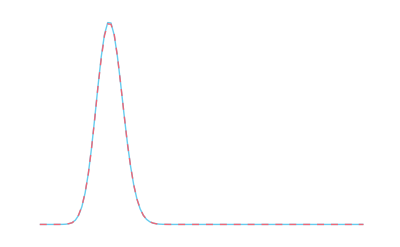

```mathematica
(* generate tt samples *)
tt=400000;
ff=Count[RandomChoice[ps->Range[0,n],tt],#]&/@Range[0,n]/tt//N;
ListPlot[{ps,ff},Joined->True, PlotRange->All,ImageSize->a4longside/2]
```

```mathematica
-tt*hh[ff,ps]
```

881.788

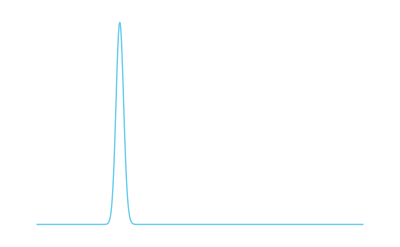

```mathematica
(* check generating with four moments and assuming two moments *)
ll={20,-3000,1700,1600};
pss=N[(#/Total@#)&@Table[Binomial[nn,ss]*Exp[Sum[cc[r,ss]*ll[[r]],{r,1,4}]],{ss,0,nn}]];

(*pss2=N[(#/Total@#)&@Table[Binomial[nn,ss]*Exp[Sum[cc[r,ss]*ll[[r]],{r,1,2}]],{ss,0,nn}]];*)ListPlot[T@{Range[0,nn]/nn,pss},Joined->True, PlotRange->All,ImageSize->a4longside/2]
```

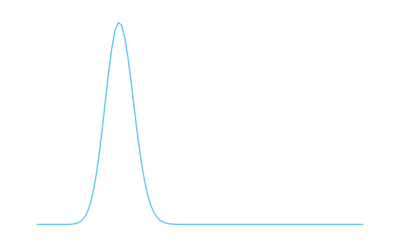

```mathematica
ps=(#/Total@#)&@Table[Sum[gg[s,ss]*pss[[ss+1]],{ss,0,nn}],{s,0,n}];
(*ps2=(#/Total@#)&@Table[Sum[gg[s,ss]*pss2[[ss+1]],{ss,0,nn}],{s,0,n}];*)
ListPlot[T@{Range[0,n]/n,ps},Joined->True, PlotRange->All,ImageSize->a4longside/2]
```

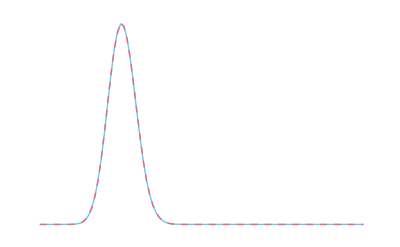

```mathematica
(* generate tt samples *)
tt=400000;
ff=Count[RandomChoice[ps->Range[0,n],tt],#]&/@Range[0,n]/tt//N;
ListPlot[{ps,ff},Joined->True, PlotRange->All,ImageSize->a4longside/2]
```

```mathematica
-tt*hh[ff,ps]
```

-424.616

```mathematica
ps2l[l1_,l2_]:=hh[ff,
(#/Total@#)&@Table[Sum[gg[s,ss]*
Binomial[nn,ss]*
Exp[cc[1,ss]*l1+cc[2,ss]*l2],{ss,0,nn}],
{s,0,n}]];
```

```mathematica
min=NMinimize[ps2l[l1,l2],{l1,l2},MaxIterations->10000,PrecisionGoal->3,Method->Automatic,AccuracyGoal->Infinity,WorkingPrecision->MachinePrecision]
```

{0.001103,{l1→-806.583,l2→-521.524}}

```mathematica
Log[10,Exp[-tt*hh[ff,ps]+tt*min[[1]]]]
```

7.20216

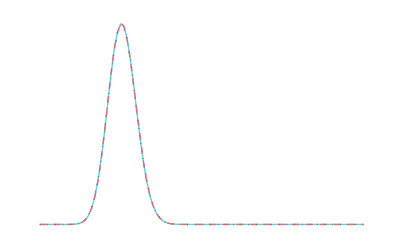

```mathematica
ListPlot[{ps,ff,(#/Total@#)&@Table[Sum[gg[s,ss]*
Binomial[nn,ss]*
(Exp[cc[1,ss]*l1+cc[2,ss]*l2]/.min[[2]]),{ss,0,nn}],
{s,0,n}]},Joined->True, PlotRange->All,ImageSize->a4longside/2]
```

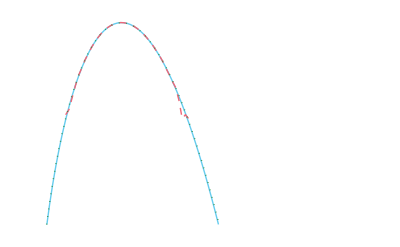

```mathematica
ListLogPlot[{ps,ff,(#/Total@#)&@Table[Sum[gg[s,ss]*
Binomial[nn,ss]*
(Exp[cc[1,ss]*l1+cc[2,ss]*l2]/.min[[2]]),{ss,0,nn}],
{s,0,n}]},Joined->True, PlotRange->{10^-10,All},ImageSize->a4longside/2]
```

```mathematica
ps4l[l1_,l2_,l3_,l4_]:=hh[ff,
(#/Total@#)&@Table[Sum[gg[s,ss]*
Binomial[nn,ss]*
Exp[cc[1,ss]*l1+cc[2,ss]*l2+cc[3,ss]*l3+cc[4,ss]*l4],{ss,0,nn}],
{s,0,n}]];
```

```mathematica
NMinimize[ps4l[l1,l2,l3,l4],{l1,l2,l3,l4},MaxIterations->10000,PrecisionGoal->3,Method->Automatic,AccuracyGoal->Infinity,WorkingPrecision->MachinePrecision]
```

{0.000820616,{l1→-851.121,l2→-464.327,l3→211.457,l4→-977.6}}

```mathematica
tt*0.0008206159376574157
```

328.246

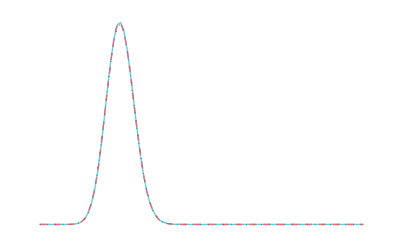

```mathematica
ListPlot[{ps,ff,(#/Total@#)&@Table[Sum[gg[s,ss]*
Binomial[nn,ss]*
Exp[cc[1,ss]*(-834.8920079079007)+cc[2,ss]*(-538.8590899358828)],{ss,0,nn}],
{s,0,n}]},Joined->True, PlotRange->All,ImageSize->a4longside/2]
```

```mathematica
cc[r_,ss_]=Binomial[ss,r];
```

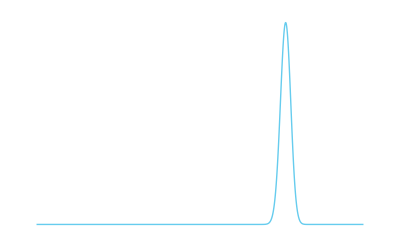

```mathematica
(* check with two moments *)
ll={0.02,0.0015};
pss=N[(#/Total@#)&@Table[Binomial[nn,ss]*Exp[Sum[cc[r,ss]*ll[[r]],{r,1,2}]],{ss,0,nn}]];ListPlot[T@{Range[0,nn]/nn,pss},Joined->True, PlotRange->All,ImageSize->a4longside/2]
```

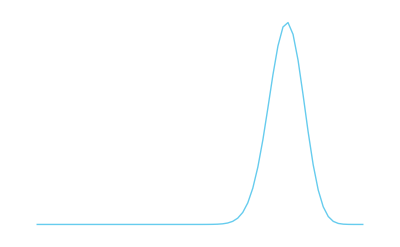

```mathematica
ps=(#/Total@#)&@Table[Sum[gg[s,ss]*pss[[ss+1]],{ss,0,nn}],{s,0,n}];
ListPlot[T@{Range[0,n]/n,ps},Joined->True, PlotRange->All,ImageSize->a4longside/2]
```

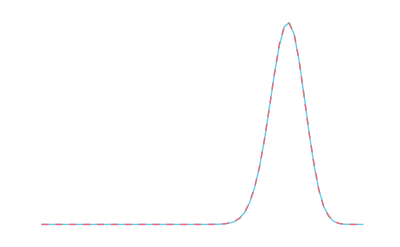

```mathematica
(* generate tt samples *)
ffe=Count[RandomChoice[ps->Range[0,n],tt],#]&/@Range[0,n]/tt//N;
ListPlot[{ps,ffe},Joined->True, PlotRange->All,ImageSize->a4longside/2]
```

```mathematica
-tt*hh[ffe,ps]
```

-683.469

```mathematica
nonzeroe=Flatten@Position[ffe,n_/;n>0];
ffne=ffe[[nonzeroe]];
```

```mathematica
logpr=-tt*hh[ffne,
(#/Total@#)&@Table[Sum[gg[s,ss]*
Binomial[nn,ss]*
Exp[cc[1,ss]*l1+cc[2,ss]*l2+cc[3,ss]*l3+cc[4,ss]*l4],{ss,0,nn}],
{s,nonzeroe-1}]];
```

```mathematica
<<"mcmc.m";
```

```mathematica
bo=0.001;mcmc=MCMC[logpr,{{l1,-0.01,0.01,Reals},{l2,-bo,bo,Reals},{l3,-bo,bo,Reals},{l4,-bo,bo,Reals}},1000(*,"ProgressMonitor"->None*)]
```

MCMCResult[{l1→-0.0396181,l2→0.000234975,l3→0.00127217,l4→-0.000023126},«1000»]

```mathematica
valuese=mcmc["ParameterRun"];
```

```mathematica
rge={Min@#,Max@#}&@Flatten[valuese]
```

{-0.0396181,0.00280546}

```mathematica
meanse=Mean[valuese]
```

{-0.0381361,0.000906782,0.000979358,-0.000045343}

```mathematica
(corre=Mean[((T@{#-meanse}).{#-meanse})&/@valuese])//MF
```

(0.0000142186 | 1.32912×10^-6 | -1.61629×10^-6 | -4.37912×10^-7
1.32912×10^-6 | 1.26873×10^-6 | -4.33261×10^-7 | 1.29161×10^-8
-1.61629×10^-6 | -4.33261×10^-7 | 2.54151×10^-7 | 3.72561×10^-8
-4.37912×10^-7 | 1.29161×10^-8 | 3.72561×10^-8 | 1.7678×10^-8)

```mathematica
ll
```

{0.02,0.0015}

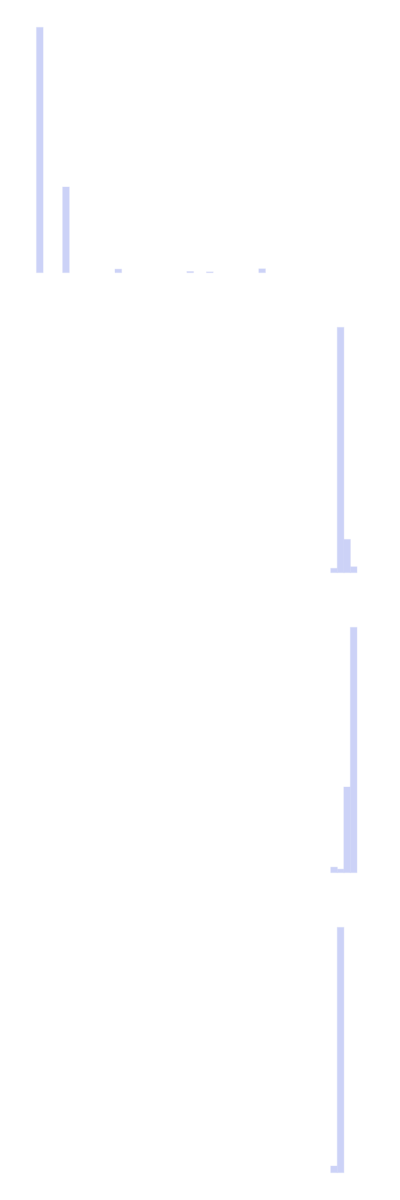
(-Graphics-)

```mathematica
bins=Flatten[{rge,Abs@Differences[rge]/50}];Table[Histogram[valuese[[;;,lx]],bins,"PDF",ImageSize->a4longside/1.75,PlotRange->{rge,All}],{lx,4}]//MF
```

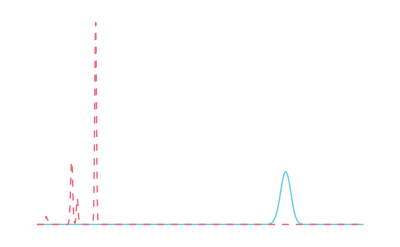

```mathematica
(* check generating with four moments and assuming two moments *)
pssr=Sum[N[(#/Total@#)&@Table[Binomial[nn,ss]*Exp[Sum[cc[r,ss]*valuese[[kk,r]],{r,1,4}]],{ss,0,nn}]],{kk,Length[valuese]}]/Length[valuese];

(*pss2=N[(#/Total@#)&@Table[Binomial[nn,ss]*Exp[Sum[cc[r,ss]*ll[[r]],{r,1,2}]],{ss,0,nn}]];*)ListPlot[{pss,pssr},Joined->True, PlotRange->All,ImageSize->a4longside/2]
```

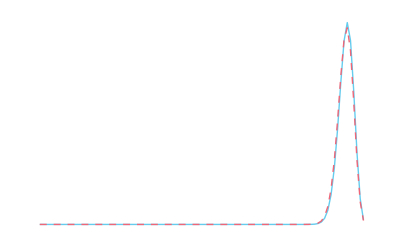

```mathematica
psr=(#/Total@#)&@Table[Sum[gg[s,ss]*pssr[[ss+1]],{ss,0,nn}],{s,0,n}];
(*ps2=(#/Total@#)&@Table[Sum[gg[s,ss]*pss2[[ss+1]],{ss,0,nn}],{s,0,n}];*)
ListPlot[{ps,psr},Joined->True, PlotRange->All,ImageSize->a4longside/2]
```

```mathematica
-tt*hh[ff,psr]
```

-2070.02

```mathematica
Log[10,Exp[-tt*(hh[ff,ps]-hh[ff,psr])]]
```

619.043961817403

```mathematica
(* non-flat prior *)
```

```mathematica
logpr=-tt*hh[ffn,
(#/Total@#)&@Table[Sum[gg[s,ss]*
Binomial[nn,ss]*
Exp[cc[1,ss]*l1+cc[2,ss]*l2+cc[3,ss]*l3+cc[4,ss]*l4],{ss,0,nn}],
{s,nonzero-1}]]-nn*(l1+l2+l3+l4)^2;
```

```mathematica
<<"mcmc.m";
```

```mathematica
mcmc=MCMC[logpr,{{l1,-1000,1000,Reals},{l2,-1000,1000,Reals},{l3,0,1,Reals},{l4,0,1,Reals}},1000(*,"ProgressMonitor"->None*)]
```

MCMCResult[{l1→-3004.68,l2→2997.56,l3→-1.70333,l4→4.47987},«1000»]

```mathematica
values2=mcmc["ParameterRun"];
```

```mathematica
rg2={Max@#,Min@#}&@Flatten[values2]
```

{3373.5,-3327.71}

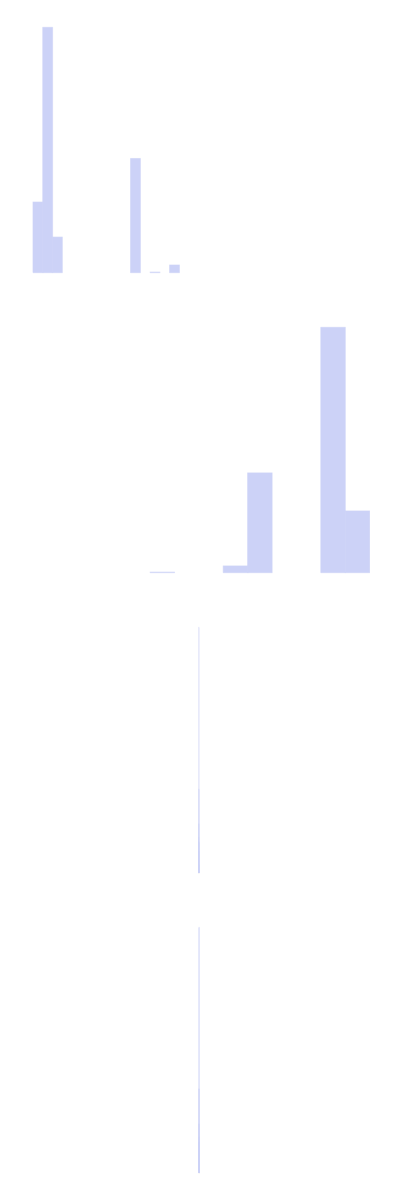
(-Graphics-)

```mathematica
Table[Histogram[values2[[;;,lx]],"Sturges","PDF",ImageSize->a4longside/2,PlotRange->{rg2,All}],{lx,4}]//MF
```

```mathematica
means2=Mean[values2]
```

{-2594.3,2601.86,-1.86236,3.25259}

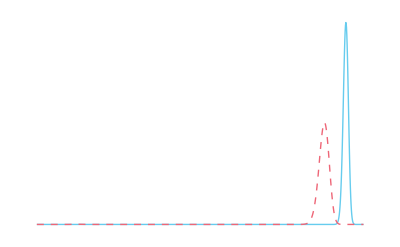

```mathematica
(* check generating with four moments and assuming two moments *)
pssr2=N[(#/Total@#)&@Table[Binomial[nn,ss]*Exp[Sum[cc[r,ss]*means2[[r]],{r,1,4}]],{ss,0,nn}]];

(*pss2=N[(#/Total@#)&@Table[Binomial[nn,ss]*Exp[Sum[cc[r,ss]*ll[[r]],{r,1,2}]],{ss,0,nn}]];*)ListPlot[{pss,pssr2},Joined->True, PlotRange->All,ImageSize->a4longside/2]
```

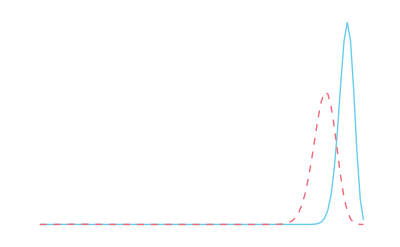

```mathematica
psr2=(#/Total@#)&@Table[Sum[gg[s,ss]*pssr2[[ss+1]],{ss,0,nn}],{s,0,n}];
(*ps2=(#/Total@#)&@Table[Sum[gg[s,ss]*pss2[[ss+1]],{ss,0,nn}],{s,0,n}];*)
ListPlot[{ps,psr2},Joined->True, PlotRange->All,ImageSize->a4longside/2]
```

```mathematica
-tt*hh[ff,psr2]
```

-943618.

```mathematica
Log[10,Exp[-tt*(hh[ff,ps]-hh[ff,psr2])]]
```

409527.998926825

```mathematica
(* Analysis as above with Stensola data *)
```

```mathematica
nn=1000;
n=65;
gg[s_,ss_]=Binomial[n,s]*Binomial[nn-n,ss-s]/Binomial[nn,ss];
```

```mathematica
cc[r_,ss_]=Binomial[ss,r]/Binomial[nn,r];
```

```mathematica
k=Flatten@Import["C:\\Users\\pglpm\\repositories\\maxNt\\scripts\\k.csv"][[2;;]];
```

```mathematica
tt=Length[k];
ff=Count[k,#]&/@Range[0,n]/tt//N;
```

```mathematica
ff
```

{0.497011,0.302466,0.127827,0.049794,0.0166195,0.0047457,0.00121396,0.00026099,0.0000550712,7.1832×10^-6,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
nonzero=Flatten@Position[ff,n_/;n>0];
ffn=ff[[nonzero]];
```

```mathematica
logpr=-tt*hh[ffn,
(#/Total@#)&@Table[Sum[gg[s,ss]*
Binomial[nn,ss]*
Exp[cc[1,ss]*l1+cc[2,ss]*l2+cc[3,ss]*l3+cc[4,ss]*l4],{ss,0,nn}],
{s,nonzero-1}]];
```

```mathematica
<<"mcmc.m";
```

```mathematica
mcmc=MCMC[logpr,{{l1,-1000,1000,Reals},{l2,-1000,1000,Reals},{l3,-1000,1000,Reals},{l4,-1000,1000,Reals}},1000(*,"ProgressMonitor"->None*)]
```

MCMCResult[{l1→-4443.3,l2→2551.15,l3→3180.93,l4→-1514.34},«1000»]

```mathematica
values=mcmc["ParameterRun"];
```

```mathematica
rg={Max@#,Min@#}&@Flatten[values]
```

{3268.19,-4576.54}

```mathematica
means=Mean[values]
```

{-4399.28,1599.57,1866.55,-1202.44}

```mathematica
(corr=Mean[((T@{#-means}).{#-means})&/@values])//MF
```

(48998.2 | -76320.5 | -89777.2 | 15633.1
-76320.5 | 1.81224×10^6 | 1.80626×10^6 | -365261.
-89777.2 | 1.80626×10^6 | 2.54371×10^6 | -425748.
15633.1 | -365261. | -425748. | 153027.)

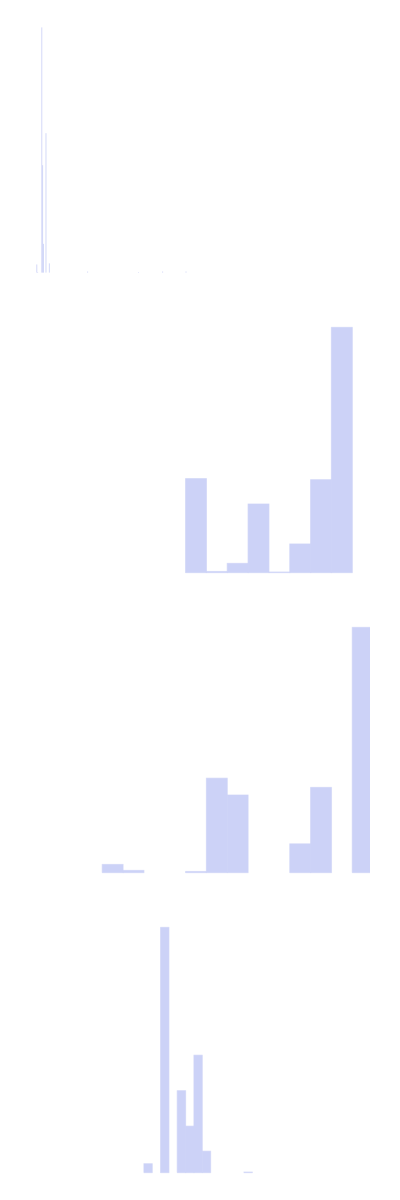
(-Graphics-)

```mathematica
Table[Histogram[values[[;;,lx]],"FreedmanDiaconis","PDF",ImageSize->a4longside/1.75,PlotRange->{rg,All}],{lx,4}]//MF
```

```mathematica
means=Mean[values]
```

{-1954.16,2526.19,1.0662,1.19121}

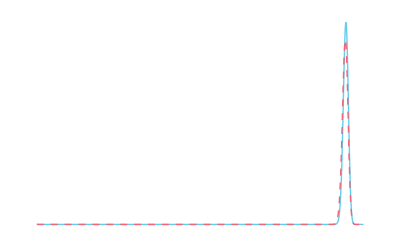

```mathematica
(* check generating with four moments and assuming two moments *)
pssr=N[(#/Total@#)&@Table[Binomial[nn,ss]*Exp[Sum[cc[r,ss]*means[[r]],{r,1,4}]],{ss,0,nn}]];

(*pss2=N[(#/Total@#)&@Table[Binomial[nn,ss]*Exp[Sum[cc[r,ss]*ll[[r]],{r,1,2}]],{ss,0,nn}]];*)ListPlot[{pss,pssr},Joined->True, PlotRange->All,ImageSize->a4longside/2]
```

```mathematica
psr=(#/Total@#)&@Table[Sum[gg[s,ss]*pssr[[ss+1]],{ss,0,nn}],{s,0,n}];
(*ps2=(#/Total@#)&@Table[Sum[gg[s,ss]*pss2[[ss+1]],{ss,0,nn}],{s,0,n}];*)
ListPlot[{ps,psr},Joined->True, PlotRange->All,ImageSize->a4longside/2]
```

-Graphics-

```mathematica
-tt*hh[ff,psr]
```

-2070.02

```mathematica
{Max@#,Min@#}&@Flatten[mcmc["ParameterRun"][[;;]]]
```

{1.01063,-39.2124}

```mathematica
mparp=Exp@mcmc["ParameterRun"][[;;]];
```

```mathematica
(* Comparison of prediction of 3rd and 2nd normalized factorial moment for different N *)
```

```mathematica
(* stensola empirical moments *)
n=65;
all=Flatten@Import["stensola_norm_binomeans.csv"][[2;;]];
{em1,em2,em3,em4}=all
```

{0.0124204,0.000216286,4.59777×10^-6,1.07013×10^-7}

```mathematica
(* stensola *)
which="stensola"; moms=2;
nns=Table[i*1000,{i,10}];
predicted=Table[
<<(which<>ToString[moms]<>"mom_"<>ToString[nns[[i]]]<>".m");
distr=solution[[moms+1]];size=nns[[i]];
{pm1,pm2,pm3,pm4}=
Table[(distr.(Binomial[#,r]&/@Range[0,size]))/Binomial[size,r]
,{r,4}]
,{i,10}];
```

```mathematica
predicted
```

{{0.0124202497,0.00021620161,0.0000631357,0.000060443802},{0.0124202989,0.00021623213,0.00006391124,0.00006124578},{0.0124201673,0.00021611058,0.00006403935,0.00006138427},{0.012420325,0.0002162562,0.00006430674,0.00006165429},{0.0124196715,0.0002156124,0.00006374534,0.00006110344},{0.0124196095,0.0002155277,0.00006371056,0.00006107145},{0.012419537,0.0002154701,0.00006368935,0.0000610522},{0.012419264,0.0002151905,0.00006343957,0.00006080679},{0.012419451,0.0002153895,0.00006365702,0.00006102254},{0.012418974,0.0002149066,0.00006319637,0.00006056838}}

```mathematica
errors=(((all/#)&/@predicted)-1)*100
```

{{0.00108057,0.0389313,-92.7176,-99.823},{0.00068392,0.0248095,-92.806,-99.8253},{0.00174359,0.0810688,-92.8204,-99.8257},{0.0004741,0.0136683,-92.8503,-99.8264},{0.00573601,0.312291,-92.7873,-99.8249},{0.0062354,0.351734,-92.7834,-99.8248},{0.00681761,0.378568,-92.781,-99.8247},{0.00902117,0.508964,-92.7525,-99.824},{0.00751082,0.416108,-92.7773,-99.8246},{0.0113561,0.641747,-92.7246,-99.8233}}

```mathematica
(* riehle empirical moments *)
activityseq=Round[Flatten[Import["popact_SANA_bin3.npy","Table"]]];
n=159;
all=Table[N@Mean[Binomial[activityseq,r]/Binomial[n,r]],{r,4}]
{em1,em2,em3,em4}=all
```

{0.0498669,0.00261369,0.000145633,8.76024×10^-6}

{0.0498669,0.00261369,0.000145633,8.76024×10^-6}

```mathematica
which="riehle"; moms=2;
nns=Table[i*1000,{i,10}];
predicted=Table[
<<(which<>ToString[moms]<>"mom_"<>ToString[nns[[i]]]<>".m");
distr=solution[[moms+1]];size=nns[[i]];
{pm1,pm2,pm3,pm4}=
Table[(distr.(Binomial[#,r]&/@Range[0,size]))/Binomial[size,r]
,{r,4}]
,{i,10}];
```

```mathematica
predicted
```

{{0.0498666868,0.00261353332,0.00023788344,0.00011231327},{0.0498668823,0.0026137012,0.00024769744,0.0001231583},{0.049866244,0.0026131013,0.00025034409,0.0001261787},{0.049866136,0.00261298,0.0002518334,0.000127846},{0.049866325,0.0026132829,0.0002530963,0.0001291981},{0.049866558,0.0026132385,0.0002536691,0.0001298412},{0.049865413,0.0026122704,0.0002532226,0.0001294902},{0.049866628,0.0026135385,0.0002547797,0.0001310241},{0.049865195,0.0026120513,0.0002536252,0.0001299686},{0.049864793,0.0026116507,0.0002534576,0.0001298429}}

```mathematica
errors=(((all/#)&/@predicted)-1)*100
```

{{0.00050769,0.00584023,-38.7798,-92.2002},{0.000115643,-0.000581819,-41.2054,-92.887},{0.00139575,0.0223735,-41.827,-93.0573},{0.00161271,0.027017,-42.171,-93.1478},{0.00123229,0.0154216,-42.4596,-93.2195},{0.000766553,0.0171233,-42.5895,-93.2531},{0.00306119,0.0541891,-42.4883,-93.2348},{0.000625224,0.00564381,-42.8398,-93.314},{0.00349851,0.0625804,-42.5796,-93.2597},{0.00430649,0.0779316,-42.5416,-93.2532}}